# General Eco-Coevolutionary Framework for Transitions from Antagonism to Mutualism

```mathematica
Clear["Global`*"]
```

### Ecological dynamics of one-host species community (Eq. 5)

```mathematica
(* Ecological parameters (subscripts dropped for convenience) *)
param={g->1,q->1,b->2.5,v->2.5,S->0.1,h->0.5,e->0.5,δ->1};

(* Ecological dynamics *)
dHdt=g H(1-q H)+((b v F)/(S+v F))H-h v F H;
dFdt=e h v F H-δ F;

(* Equilibria *)
eq=Simplify[Solve[{dHdt==0,dFdt==0},{H,F}]];

(* Coexistence equilibrium *)
ecoCoex=eq[[2]];
ecoCoex/.param

(* Plot population dynamics *)
dHt=H'[t]==g H[t](1-q H[t])+((b v F[t])/(S+v F[t]))H[t]-h F[t] H[t];
dFt=F'[t]==e h v F[t] H[t]-δ F[t];
eqsol=NDSolve[{dHt/.param,dFt/.param,H[0]==1,F[0]==0.5},{H[t],F[t]},{t,0,1000},MaxSteps->Infinity,AccuracyGoal->Infinity];
Plot[{H[t]/.eqsol,F[t]/.eqsol},{t,0,1000},PlotRange->{{0,1000},{0,10}},PlotStyle->{{Black,Thick},{Blue,Thick}},Frame->True,FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},LabelStyle->Directive[FontSize->20]];
```

{H→1.6,F→1.46691}

### Eco-coevolutionary dynamics (Eqs. 5-8)

#### Resident ancestral interaction (Eq. 5-6)

```mathematica
(* Parameters *)
param={g->1,q->1,S->0.1,δ->1,bMax->5,vMax->5,hMax->2,eMax->1,xB->0,xV->0,xH->0,yV->0,yH->0,bS->1,vS->1,hS->1,cFv->0.5,cFh->0.5};

(* Ecological dynamics (Eq. 5) *)
dHdt=g H(1-q H)+((bf vf F)/(S+vf F))H-hf vf F H;
dFdt=ef hf vf F H-δ F;

(* Equilibria *)
eq=Simplify[Solve[{dHdt==0,dFdt==0},{H,F}]];

(* Trait functions *)
(* Note: bS, vS, hS used instead of B', V', H' in manuscript *)
(* Note: cFv, cFh used instead of c^V_F, c^H_F in manuscript *)
bf=bMax(2/(1+Exp[-bS xB])-1); (* Eq. 6a *)
vf=vMax/(1+Exp[-vS(xV+yV)]); (* Eq. 6b *)
hf=hMax/(1+Exp[hS(xH-yH)]); (* Eq. 6c *)
ef=eMax Exp[-(cFv yV^2+cFh yH^2)]; (* Eq. 6d *)

(* Coexistence equilibrium *)
coex=eq[[2]];
coex/.param
```

{H→0.4,F→0.24}

#### Invasion fitness and selection gradients (Eq. 8)

```mathematica
(* Invasion fitness *)
(* Host *)
(* Note: cHb, cHv, cHh used instead of c^B_H, c^V_H, c^H_H in manuscript *)
Wh=g(1-qf H)+((bMax(2/(1+Exp[-bS xBmut])-1)(vMax/(1+Exp[-vS(xVmut+yV)])) F)/(S+(vMax/(1+Exp[-vS(xVmut+yV)])) F))-(hMax/(1+Exp[hS(xHmut-yH)])) F; (*Eq. 8a*)
qf=(1+cHb (xBmut^sB-xB^sB)+cHv (xVmut^sV-xV^sV)+cHh(xHmut^sH-xH^sH)); (*Eq. 8c*)
(* Focal Partner *)
Wf=(eMax Exp[-(cFv yVmut^2+cFh yHmut^2)])(vMax/(1+Exp[-vS(xV+yVmut)]))(hMax/(1+Exp[hS(xH-yHmut)])) H-δ; (*Eq. 8b*)

(* Selection Gradients *)
(* Host *)
dxBdt=D[Wh,xBmut]/.coex/.xBmut->xB/.xVmut->xV/.xHmut->xH;
dxVdt=D[Wh,xVmut]/.coex/.xBmut->xB/.xVmut->xV/.xHmut->xH;
dxHdt=D[Wh,xHmut]/.coex/.xBmut->xB/.xVmut->xV/.xHmut->xH;
(* Focal Partner *)
dyVdt=D[Wf,yVmut]/.coex/.yVmut->yV/.yHmut->yH;
dyHdt=D[Wf,yHmut]/.coex/.yVmut->yV/.yHmut->yH;
```

#### Simulate evolutionary dynamics (for linear and convex trade-offs (s ≥ 1), use cell below for concave)

##### Note: The error “NDSolve: The function value ... is not a real number when the arguments are ... ” indicates evolutionary purging of the partner. The error occurs because the partner equilibrium becomes an imaginary number when it is extinct. To avoid evolutionary purging, try varying the value of cHv and/or cHh or increasing vMax Note: If host evolves zero defense, try increasing hMax

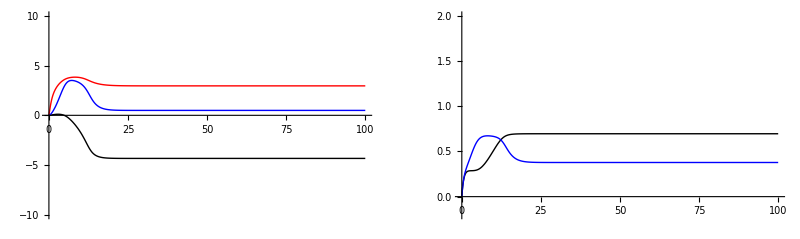

xB: 2.96289 xV: -4.33567 xH: 0.494424

yV: 0.696008 yH: 0.377923

b: 4.50869 v: 0.179124 h: 2.35454

e: 0.644631 Equilibrium: {{H→3.67815,F→2.06676}}

```mathematica
(* Evolutionary parameters *)
(* Note: For ancestral interaction, set bMax = 0, cHb = 0, and cHv = 0 *)
evoParam={g->1,q->1,S->0.1,δ->1,bMax->5,vMax->7,hMax->5,eMax->1,bS->1,vS->1,hS->1,sB->1,sV->1,sH->1,cHb->0.1,cHv->0.2,cHh->0.7,cFv->0.7,cFh->0.7};
end=100; (* how long to run eco-evolutionary model *)

(* Evolutionary dynamics *)
Off[NDSolve::nrnum1]
Off[NDSolve::evcvmit]
Off[InterpolatingFunction::dmval]
dxBt=xB'[T]==-(cHb ⅇ^(cFh yH[T]^2+cFv yV[T]^2) (1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))) g sB xB[T]^(-1+sB) δ)/(hMax vMax eMax)+(bMax bS ⅇ^(-bS xB[T]+cFh yH[T]^2+cFv yV[T]^2) (1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T])))^2 ((hMax bMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) (-1+2/(1+ⅇ^(-bS xB[T]))) vMax^2 eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T])))^2)+(hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax^2 eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T])))^2)-(hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax^2 S eMax)/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T])))^2)-(g vMax q δ)/(1+ⅇ^(-vS (xV[T]+yV[T])))+√(1/((1+ⅇ^(-vS (xV[T]+yV[T])))^2)vMax^2 ((4 hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax S eMax ((hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))-q δ))/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T]))))+((hMax bMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) (-1+2/(1+ⅇ^(-bS xB[T]))) vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))+(hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))-(hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax S eMax)/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T]))))-g q δ)^2))))/(hMax^2 (1+ⅇ^(-bS xB[T]))^2 vMax^2 eMax (S+1/(2 hMax^2 vMax^2 eMax)ⅇ^(cFh yH[T]^2+cFv yV[T]^2) (1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T])))^2 ((hMax bMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) (-1+2/(1+ⅇ^(-bS xB[T]))) vMax^2 eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T])))^2)+(hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax^2 eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T])))^2)-(hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax^2 S eMax)/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T])))^2)-(g vMax q δ)/(1+ⅇ^(-vS (xV[T]+yV[T])))+√(1/((1+ⅇ^(-vS (xV[T]+yV[T])))^2)vMax^2 ((4 hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax S eMax ((hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))-q δ))/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T]))))+((hMax bMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) (-1+2/(1+ⅇ^(-bS xB[T]))) vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))+(hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))-(hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax S eMax)/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T]))))-g q δ)^2)))));
dxVt=xV'[T]==-(cHv ⅇ^(cFh yH[T]^2+cFv yV[T]^2) (1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))) g sV xV[T]^(-1+sV) δ)/(hMax vMax eMax)-(bMax ⅇ^(2 cFh yH[T]^2+2 cFv yV[T]^2-vS (xV[T]+yV[T])) (1+ⅇ^(hS (xH[T]-yH[T])))^4 (1+ⅇ^(-vS (xV[T]+yV[T])))^3 (-1+2/(1+ⅇ^(-bS xB[T]))) vS ((hMax bMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) (-1+2/(1+ⅇ^(-bS xB[T]))) vMax^2 eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T])))^2)+(hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax^2 eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T])))^2)-(hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax^2 S eMax)/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T])))^2)-(g vMax q δ)/(1+ⅇ^(-vS (xV[T]+yV[T])))+√(1/((1+ⅇ^(-vS (xV[T]+yV[T])))^2)vMax^2 ((4 hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax S eMax ((hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))-q δ))/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T]))))+((hMax bMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) (-1+2/(1+ⅇ^(-bS xB[T]))) vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))+(hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))-(hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax S eMax)/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T]))))-g q δ)^2)))^2)/(4 hMax^4 vMax^4 eMax^2 (S+1/(2 hMax^2 vMax^2 eMax)ⅇ^(cFh yH[T]^2+cFv yV[T]^2) (1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T])))^2 ((hMax bMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) (-1+2/(1+ⅇ^(-bS xB[T]))) vMax^2 eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T])))^2)+(hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax^2 eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T])))^2)-(hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax^2 S eMax)/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T])))^2)-(g vMax q δ)/(1+ⅇ^(-vS (xV[T]+yV[T])))+√(1/((1+ⅇ^(-vS (xV[T]+yV[T])))^2)vMax^2 ((4 hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax S eMax ((hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))-q δ))/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T]))))+((hMax bMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) (-1+2/(1+ⅇ^(-bS xB[T]))) vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))+(hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))-(hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax S eMax)/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T]))))-g q δ)^2))))^2)+(bMax ⅇ^(cFh yH[T]^2+cFv yV[T]^2-vS (xV[T]+yV[T])) (1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T]))) (-1+2/(1+ⅇ^(-bS xB[T]))) vS ((hMax bMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) (-1+2/(1+ⅇ^(-bS xB[T]))) vMax^2 eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T])))^2)+(hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax^2 eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T])))^2)-(hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax^2 S eMax)/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T])))^2)-(g vMax q δ)/(1+ⅇ^(-vS (xV[T]+yV[T])))+√(1/((1+ⅇ^(-vS (xV[T]+yV[T])))^2)vMax^2 ((4 hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax S eMax ((hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))-q δ))/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T]))))+((hMax bMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) (-1+2/(1+ⅇ^(-bS xB[T]))) vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))+(hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))-(hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax S eMax)/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T]))))-g q δ)^2))))/(2 hMax^2 vMax^2 eMax (S+1/(2 hMax^2 vMax^2 eMax)ⅇ^(cFh yH[T]^2+cFv yV[T]^2) (1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T])))^2 ((hMax bMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) (-1+2/(1+ⅇ^(-bS xB[T]))) vMax^2 eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T])))^2)+(hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax^2 eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T])))^2)-(hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax^2 S eMax)/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T])))^2)-(g vMax q δ)/(1+ⅇ^(-vS (xV[T]+yV[T])))+√(1/((1+ⅇ^(-vS (xV[T]+yV[T])))^2)vMax^2 ((4 hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax S eMax ((hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))-q δ))/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T]))))+((hMax bMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) (-1+2/(1+ⅇ^(-bS xB[T]))) vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))+(hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))-(hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax S eMax)/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T]))))-g q δ)^2)))));
dxHt=xH'[T]==-1/(hMax vMax eMax)cHh ⅇ^(cFh yH[T]^2+cFv yV[T]^2) (1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))) g sH δ xH[T]^(-1+sH)+1/(2 hMax vMax^3 eMax)hS ⅇ^(hS (xH[T]-yH[T])+cFh yH[T]^2+cFv yV[T]^2) (1+ⅇ^(-vS (xV[T]+yV[T])))^3 ((hMax bMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) (-1+2/(1+ⅇ^(-bS xB[T]))) vMax^2 eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T])))^2)+(hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax^2 eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T])))^2)-(hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax^2 S eMax)/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T])))^2)-(g vMax q δ)/(1+ⅇ^(-vS (xV[T]+yV[T])))+√(1/((1+ⅇ^(-vS (xV[T]+yV[T])))^2)vMax^2 ((4 hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax S eMax ((hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))-q δ))/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T]))))+((hMax bMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) (-1+2/(1+ⅇ^(-bS xB[T]))) vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))+(hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))-(hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax S eMax)/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T]))))-g q δ)^2)));
dyVt=yV'[T]==(ⅇ^(-vS (xV[T]+yV[T])) vS δ)/(1+ⅇ^(-vS (xV[T]+yV[T])))-2 cFv yV[T] δ;
dyHt=yH'[T]==(hS ⅇ^(hS (xH[T]-yH[T])) δ)/(1+ⅇ^(hS (xH[T]-yH[T])))-2 cFh yH[T] δ;
eqsolEvo=NDSolve[{dxBt/.evoParam,dxVt/.evoParam,dxHt/.evoParam,dyVt/.evoParam,dyHt/.evoParam,xB[0]==0.0001,xV[0]==0.0001,xH[0]==0.0001,yV[0]==0,yH[0]==0,WhenEvent[Im[xV[T]]≠0,{"StopIntegration",end=T,Print["Host purges partner"]}]},{xB,xV,xH,yV,yH},{T,0,end}];

(* Trait dynamics *)
GraphicsGrid[{{Plot[{xB[t]/.eqsolEvo,xV[t]/.eqsolEvo,xH[t]/.eqsolEvo},{t,0,end},PlotRange->{{0,end},{-10,10}},PlotStyle->{{Red,Thick},{Black,Thick},{Blue,Thick}},TicksStyle->Black,AxesStyle->Black,LabelStyle->Directive[FontSize->12]],
Plot[{yV[t]/.eqsolEvo,yH[t]/.eqsolEvo},{t,0,end},PlotRange->{{0,end},{-0.2,2}},PlotStyle->{{Black,Thick},{Blue,Thick}},TicksStyle->Black,AxesStyle->Black,LabelStyle->Directive[FontSize->12]]}}]

(* Trait coESS *)
Print["xB: ",(xB[end]/.eqsolEvo)[[1]]," xV: ",(xV[end]/.eqsolEvo)[[1]]," xH: ",(xH[end]/.eqsolEvo)[[1]]]
Print["yV: ",(yV[end]/.eqsolEvo)[[1]]," yH: ",(yH[end]/.eqsolEvo)[[1]]]

(* Trait functions *)
Print["b: ",(bf/.evoParam/.xB->xB[end]/.xV->xV[end]/.xH->Max[0,xH[end]]/.yV->yV[end]/.yH->yH[end]/.eqsolEvo)[[1]]," v: ",(vf/.evoParam/.xB->xB[end]/.xV->xV[end]/.xH->Max[0,xH[end]]/.yV->yV[end]/.yH->yH[end]/.eqsolEvo)[[1]]," h: ",(hf/.evoParam/.xB->xB[end]/.xV->xV[end]/.xH->Max[0,xH[end]]/.yV->yV[end]/.yH->yH[end]/.eqsolEvo)[[1]]]
Print["e: ",(ef/.evoParam/.xB->xB[end]/.xV->xV[end]/.xH->Max[0,xH[end]]/.yV->yV[end]/.yH->yH[end]/.eqsolEvo)[[1]],
" Equilibrium: ",(coex/.evoParam/.xB->xB[end]/.xV->xV[end]/.xH->Max[0,xH[end]]/.yV->yV[end]/.yH->yH[end]/.eqsolEvo/.eqsolEvo)[[1]]]
```

#### Fig S3a) Systematically vary host costs for linear trade-off (run cell above and update “outcome” table)

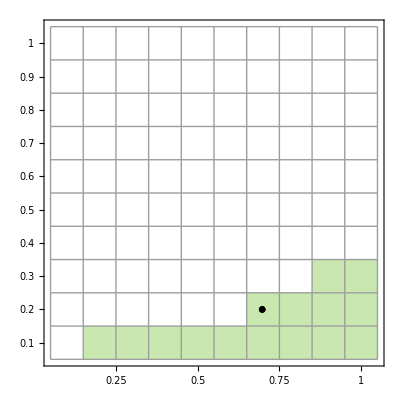

```mathematica
(* cHh from left-to-right, cHv from bottom-to-top *)
(* 0 = transition to mutualism, -1 = partner purged, 1 = antagonism *)
outcome={{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},
{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},
{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},
{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},
{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},
{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},
{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},
{-1,-1,-1,-1,-1,-1,-1,-1,0,0},
{-1,-1,-1,-1,-1,-1,0,0,0,0},
{-1,0,0,0,0,0,0,0,0,0}};

(* Plot *)
Show[MatrixPlot[Reverse[outcome],AspectRatio->1,ColorRules->{-1->White,0->RGBColor[201/255,232/255,176/255],1->Gray},DataReversed->True,FrameStyle->Black,LabelStyle->Directive[FontSize->20],Mesh->True,FrameTicks->{{{{1,0.1},{2,0.2},{3,0.3},{4,0.4},{5,0.5},{6,0.6},{7,0.7},{8,0.8},{9,0.9},{10,1}},None},{{{0,0},{2.5,0.25},{5,0.5},{7.5,0.75},{10,1}},None}}],
ListPlot[{{9.25 0.7,7.5 0.2}},PlotMarkers->{Graphics[{EdgeForm[{Black,Thick}],FaceForm[Black],Disk[]}],0.05}]]
```

#### Fig S3b) Systematically vary host costs for convex trade-off (run cell above and update “outcome” table)

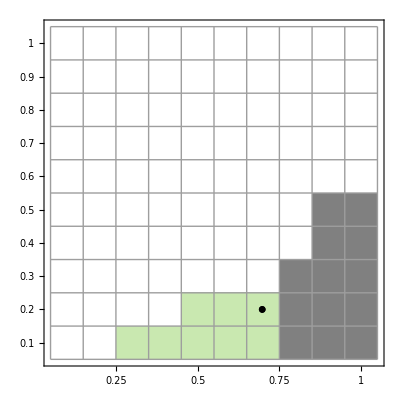

```mathematica
(* cHh from left-to-right, cHv from bottom-to-top *)
(* 0 = transition to mutualism, -1 = partner purged, 1 = antagonism *)
outcome={{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},
{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},
{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},
{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},
{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},
{-1,-1,-1,-1,-1,-1,-1,-1,1,1},
{-1,-1,-1,-1,-1,-1,-1,-1,1,1},
{-1,-1,-1,-1,-1,-1,-1,1,1,1},
{-1,-1,-1,-1,0,0,0,1,1,1},
{-1,-1,0,0,0,0,0,1,1,1}};

(* Plot *)
Show[MatrixPlot[Reverse[outcome],AspectRatio->1,ColorRules->{-1->White,0->RGBColor[201/255,232/255,176/255],1->Gray},DataReversed->True,FrameStyle->Black,LabelStyle->Directive[FontSize->20],Mesh->True,FrameTicks->{{{{1,0.1},{2,0.2},{3,0.3},{4,0.4},{5,0.5},{6,0.6},{7,0.7},{8,0.8},{9,0.9},{10,1}},None},{{{0,0},{2.5,0.25},{5,0.5},{7.5,0.75},{10,1}},None}}],
ListPlot[{{9.25 0.7,7.5 0.2}},PlotMarkers->{Graphics[{EdgeForm[{Black,Thick}],FaceForm[Black],Disk[]}],0.05}]]
```

#### Fig S3d) Systematically vary partner costs for linear trade-off (run cell above and update “outcome” table)

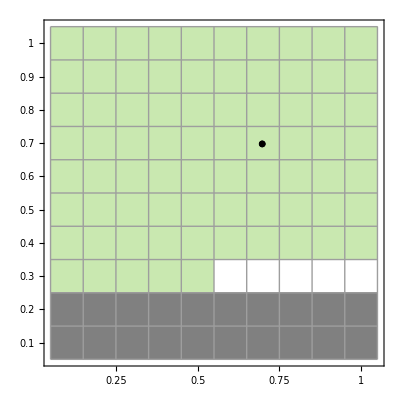

```mathematica
(* cFh from left-to-right, cFv from bottom-to-top *)
(* 0 = transition to mutualism, -1 = partner purged, 1 = antagonism *)
outcome={{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,-1,-1,-1,-1,-1},
{1,1,1,1,1,1,1,1,1,1},
{1,1,1,1,1,1,1,1,1,1}};

(* Plot *)
Show[MatrixPlot[Reverse[outcome],AspectRatio->1,ColorRules->{-1->White,0->RGBColor[201/255,232/255,176/255],1->Gray},DataReversed->True,FrameStyle->Black,LabelStyle->Directive[FontSize->20],Mesh->True,FrameTicks->{{{{1,0.1},{2,0.2},{3,0.3},{4,0.4},{5,0.5},{6,0.6},{7,0.7},{8,0.8},{9,0.9},{10,1}},None},{{{0,0},{2.5,0.25},{5,0.5},{7.5,0.75},{10,1}},None}}],
ListPlot[{{9.25 0.7,9.25 0.7}},PlotMarkers->{Graphics[{EdgeForm[{Black,Thick}],FaceForm[Black],Disk[]}],0.05}]]
```

#### Fig S3e) Systematically vary partner costs for convex trade-off (run cell above and update “outcome” table)

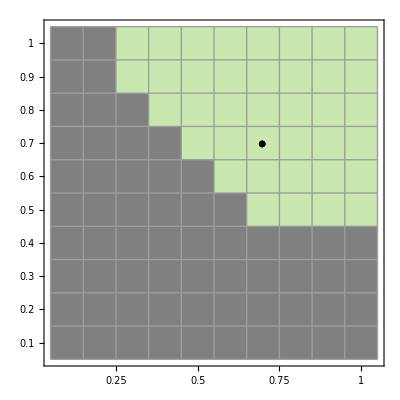

```mathematica
(* cFh from left-to-right, cFv from bottom-to-top *)
(* 0 = transition to mutualism, -1 = partner purged, 1 = antagonism *)
outcome={{1,1,0,0,0,0,0,0,0,0},
{1,1,0,0,0,0,0,0,0,0},
{1,1,1,0,0,0,0,0,0,0},
{1,1,1,1,0,0,0,0,0,0},
{1,1,1,1,1,0,0,0,0,0},
{1,1,1,1,1,1,0,0,0,0},
{1,1,1,1,1,1,1,1,1,1},
{1,1,1,1,1,1,1,1,1,1},
{1,1,1,1,1,1,1,1,1,1},
{1,1,1,1,1,1,1,1,1,1}};

(* Plot *)
Show[MatrixPlot[Reverse[outcome],AspectRatio->1,ColorRules->{-1->White,0->RGBColor[201/255,232/255,176/255],1->Gray},DataReversed->True,FrameStyle->Black,LabelStyle->Directive[FontSize->20],Mesh->True,FrameTicks->{{{{1,0.1},{2,0.2},{3,0.3},{4,0.4},{5,0.5},{6,0.6},{7,0.7},{8,0.8},{9,0.9},{10,1}},None},{{{0,0},{2.5,0.25},{5,0.5},{7.5,0.75},{10,1}},None}}],
ListPlot[{{9.25 0.7,9.25 0.7}},PlotMarkers->{Graphics[{EdgeForm[{Black,Thick}],FaceForm[Black],Disk[]}],0.05}]]
```

#### Simulate evolutionary dynamics (for concave trade-offs (s < 1), use cell above for linear and convex)

##### Note: The error “NDSolve: The function value ... is not a real number when the arguments are ... ” indicates evolutionary purging of the partner. The error occurs because the partner equilibrium becomes an imaginary number when it is extinct. To avoid evolutionary purging, try varying the value of cHh and/or cHv or increasing vMax Note: If host evolves zero defense, try increasing hMax Note: The error “Power: Infinite expression ...” occurs because the trade-off goes to -∞, which indicates that one of the traits has evolved to zero

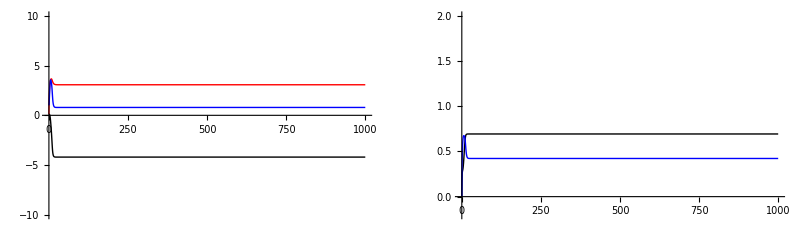

xB: 3.07431 xV: -4.20293 xH: 0.791674

yV: 0.693539 yH: 0.422353

b: 4.55821 v: 0.203323 h: 2.04353

e: 0.630297 Equilibrium: {{H→3.81847,F→2.12618}}

```mathematica
(* Evolutionary parameters *)
(* Note: For ancestral interaction, set bMax = 0, cHb = 0, and cHv = 0 *)
evoParam={g->1,q->1,S->0.1,δ->1,bMax->5,vMax->7,hMax->5,eMax->1,bS->1,vS->1,hS->1,sB->0.95,sV->0.95,sH->0.95,cHb->0.1,cHv->0.2,cHh->0.7,cFv->0.7,cFh->0.7};
plotEnd=end=1000; (* how long to run eco-evolutionary model *)

(* Evolutionary dynamics *)
Off[NDSolve::nrnum1]
Off[NDSolve::evcvmit]
Off[InterpolatingFunction::dmval]
dxBt=xB'[T]==-1/(hMax vMax eMax)cHb ⅇ^(cFh yH[T]^2+cFv yV[T]^2) (1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))) g sB δ xB[T]^(-1+sB) +(bMax bS ⅇ^(-bS xB[T]+cFh yH[T]^2+cFv yV[T]^2) (1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T])))^2 ((hMax bMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) (-1+2/(1+ⅇ^(-bS xB[T]))) vMax^2 eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T])))^2)+(hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax^2 eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T])))^2)-(hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax^2 S eMax)/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T])))^2)-(g vMax q δ)/(1+ⅇ^(-vS (xV[T]+yV[T])))+√(1/((1+ⅇ^(-vS (xV[T]+yV[T])))^2)vMax^2 ((4 hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax S eMax ((hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))-q δ))/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T]))))+((hMax bMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) (-1+2/(1+ⅇ^(-bS xB[T]))) vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))+(hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))-(hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax S eMax)/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T]))))-g q δ)^2))))/(hMax^2 (1+ⅇ^(-bS xB[T]))^2 vMax^2 eMax (S+1/(2 hMax^2 vMax^2 eMax)ⅇ^(cFh yH[T]^2+cFv yV[T]^2) (1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T])))^2 ((hMax bMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) (-1+2/(1+ⅇ^(-bS xB[T]))) vMax^2 eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T])))^2)+(hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax^2 eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T])))^2)-(hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax^2 S eMax)/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T])))^2)-(g vMax q δ)/(1+ⅇ^(-vS (xV[T]+yV[T])))+√(1/((1+ⅇ^(-vS (xV[T]+yV[T])))^2)vMax^2 ((4 hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax S eMax ((hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))-q δ))/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T]))))+((hMax bMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) (-1+2/(1+ⅇ^(-bS xB[T]))) vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))+(hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))-(hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax S eMax)/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T]))))-g q δ)^2)))));
dxVt=xV'[T]==-1/(hMax vMax eMax)cHv ⅇ^(cFh yH[T]^2+cFv yV[T]^2) (1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))) g sV δ Abs[xV[T]]^(-1+sV) (* Abs function used to prevent function from going to infinity and causing an error *)-(bMax ⅇ^(2 cFh yH[T]^2+2 cFv yV[T]^2-vS (xV[T]+yV[T])) (1+ⅇ^(hS (xH[T]-yH[T])))^4 (1+ⅇ^(-vS (xV[T]+yV[T])))^3 (-1+2/(1+ⅇ^(-bS xB[T]))) vS ((hMax bMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) (-1+2/(1+ⅇ^(-bS xB[T]))) vMax^2 eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T])))^2)+(hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax^2 eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T])))^2)-(hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax^2 S eMax)/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T])))^2)-(g vMax q δ)/(1+ⅇ^(-vS (xV[T]+yV[T])))+√(1/((1+ⅇ^(-vS (xV[T]+yV[T])))^2)vMax^2 ((4 hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax S eMax ((hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))-q δ))/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T]))))+((hMax bMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) (-1+2/(1+ⅇ^(-bS xB[T]))) vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))+(hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))-(hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax S eMax)/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T]))))-g q δ)^2)))^2)/(4 hMax^4 vMax^4 eMax^2 (S+1/(2 hMax^2 vMax^2 eMax)ⅇ^(cFh yH[T]^2+cFv yV[T]^2) (1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T])))^2 ((hMax bMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) (-1+2/(1+ⅇ^(-bS xB[T]))) vMax^2 eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T])))^2)+(hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax^2 eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T])))^2)-(hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax^2 S eMax)/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T])))^2)-(g vMax q δ)/(1+ⅇ^(-vS (xV[T]+yV[T])))+√(1/((1+ⅇ^(-vS (xV[T]+yV[T])))^2)vMax^2 ((4 hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax S eMax ((hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))-q δ))/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T]))))+((hMax bMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) (-1+2/(1+ⅇ^(-bS xB[T]))) vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))+(hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))-(hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax S eMax)/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T]))))-g q δ)^2))))^2)+(bMax ⅇ^(cFh yH[T]^2+cFv yV[T]^2-vS (xV[T]+yV[T])) (1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T]))) (-1+2/(1+ⅇ^(-bS xB[T]))) vS ((hMax bMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) (-1+2/(1+ⅇ^(-bS xB[T]))) vMax^2 eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T])))^2)+(hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax^2 eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T])))^2)-(hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax^2 S eMax)/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T])))^2)-(g vMax q δ)/(1+ⅇ^(-vS (xV[T]+yV[T])))+√(1/((1+ⅇ^(-vS (xV[T]+yV[T])))^2)vMax^2 ((4 hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax S eMax ((hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))-q δ))/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T]))))+((hMax bMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) (-1+2/(1+ⅇ^(-bS xB[T]))) vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))+(hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))-(hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax S eMax)/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T]))))-g q δ)^2))))/(2 hMax^2 vMax^2 eMax (S+1/(2 hMax^2 vMax^2 eMax)ⅇ^(cFh yH[T]^2+cFv yV[T]^2) (1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T])))^2 ((hMax bMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) (-1+2/(1+ⅇ^(-bS xB[T]))) vMax^2 eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T])))^2)+(hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax^2 eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T])))^2)-(hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax^2 S eMax)/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T])))^2)-(g vMax q δ)/(1+ⅇ^(-vS (xV[T]+yV[T])))+√(1/((1+ⅇ^(-vS (xV[T]+yV[T])))^2)vMax^2 ((4 hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax S eMax ((hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))-q δ))/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T]))))+((hMax bMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) (-1+2/(1+ⅇ^(-bS xB[T]))) vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))+(hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))-(hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax S eMax)/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T]))))-g q δ)^2)))));
dxHt=xH'[T]==-1/(hMax vMax eMax)cHh ⅇ^(cFh yH[T]^2+cFv yV[T]^2) (1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))) g sH δ xH[T]^(-1+sH)+1/(2 hMax vMax^3 eMax)hS ⅇ^(hS (xH[T]-yH[T])+cFh yH[T]^2+cFv yV[T]^2) (1+ⅇ^(-vS (xV[T]+yV[T])))^3 ((hMax bMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) (-1+2/(1+ⅇ^(-bS xB[T]))) vMax^2 eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T])))^2)+(hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax^2 eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T])))^2)-(hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax^2 S eMax)/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T])))^2)-(g vMax q δ)/(1+ⅇ^(-vS (xV[T]+yV[T])))+√(1/((1+ⅇ^(-vS (xV[T]+yV[T])))^2)vMax^2 ((4 hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax S eMax ((hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))-q δ))/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T]))))+((hMax bMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) (-1+2/(1+ⅇ^(-bS xB[T]))) vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))+(hMax ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) g vMax eMax)/((1+ⅇ^(hS (xH[T]-yH[T]))) (1+ⅇ^(-vS (xV[T]+yV[T]))))-(hMax^2 ⅇ^(-cFh yH[T]^2-cFv yV[T]^2) vMax S eMax)/((1+ⅇ^(hS (xH[T]-yH[T])))^2 (1+ⅇ^(-vS (xV[T]+yV[T]))))-g q δ)^2)));
dyVt=yV'[T]==(ⅇ^(-vS (xV[T]+yV[T])) vS δ)/(1+ⅇ^(-vS (xV[T]+yV[T])))-2 cFv yV[T] δ;
dyHt=yH'[T]==(hS ⅇ^(hS (xH[T]-yH[T])) δ)/(1+ⅇ^(hS (xH[T]-yH[T])))-2 cFh yH[T] δ;
eqsolEvo=NDSolve[{dxBt/.evoParam,dxVt/.evoParam,dxHt/.evoParam,dyVt/.evoParam,dyHt/.evoParam,xB[0]==0.1,xV[0]==0.1,xH[0]==1,yV[0]==0,yH[0]==0,WhenEvent[Im[xV[T]]≠0,{"StopIntegration",end=T,Print["Host purges partner"]}]},{xB,xV,xH,yV,yH},{T,0,end}];

(* Trait dynamics *)
GraphicsGrid[{{Plot[{xB[t]/.eqsolEvo,xV[t]/.eqsolEvo,xH[t]/.eqsolEvo},{t,0,end},PlotRange->{{0,plotEnd},{-10,10}},PlotStyle->{{Red,Thick},{Black,Thick},{Blue,Thick}},TicksStyle->Black,AxesStyle->Black,LabelStyle->Directive[FontSize->12]],
Plot[{yV[t]/.eqsolEvo,yH[t]/.eqsolEvo},{t,0,end},PlotRange->{{0,plotEnd},{-0.2,2}},PlotStyle->{{Black,Thick},{Blue,Thick}},TicksStyle->Black,AxesStyle->Black,LabelStyle->Directive[FontSize->12]]}}]

(* Trait coESS *)
Print["xB: ",(xB[end]/.eqsolEvo)[[1]]," xV: ",(xV[end]/.eqsolEvo)[[1]]," xH: ",(xH[end]/.eqsolEvo)[[1]]]
Print["yV: ",(yV[end]/.eqsolEvo)[[1]]," yH: ",(yH[end]/.eqsolEvo)[[1]]]

(* Trait functions *)
Print["b: ",(bf/.evoParam/.xB->xB[end]/.xV->xV[end]/.xH->Max[0,xH[end]]/.yV->yV[end]/.yH->yH[end]/.eqsolEvo)[[1]]," v: ",(vf/.evoParam/.xB->xB[end]/.xV->xV[end]/.xH->Max[0,xH[end]]/.yV->yV[end]/.yH->yH[end]/.eqsolEvo)[[1]]," h: ",(hf/.evoParam/.xB->xB[end]/.xV->xV[end]/.xH->Max[0,xH[end]]/.yV->yV[end]/.yH->yH[end]/.eqsolEvo)[[1]]]
Print["e: ",(ef/.evoParam/.xB->xB[end]/.xV->xV[end]/.xH->Max[0,xH[end]]/.yV->yV[end]/.yH->yH[end]/.eqsolEvo)[[1]],
" Equilibrium: ",(coex/.evoParam/.xB->xB[end]/.xV->xV[end]/.xH->Max[0,xH[end]]/.yV->yV[end]/.yH->yH[end]/.eqsolEvo/.eqsolEvo)[[1]]]
```

#### Fig S3c) Systematically vary host costs for concave trade-off (run cell above and update “outcome” table)

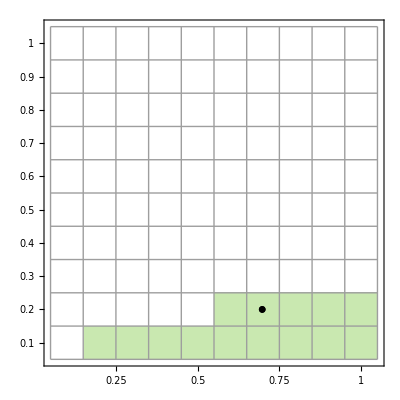

```mathematica
(* cHh from left-to-right, cHv from bottom-to-top *)
(* 0 = transition to mutualism, -1 = partner purged, 1 = antagonism *)
outcome={{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},
{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},
{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},
{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},
{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},
{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},
{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},
{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},
{-1,-1,-1,-1,-1,0,0,0,0,0},
{-1,0,0,0,0,0,0,0,0,0}};

(* Plot *)
Show[MatrixPlot[Reverse[outcome],AspectRatio->1,ColorRules->{-1->White,0->RGBColor[201/255,232/255,176/255],1->Gray},DataReversed->True,FrameStyle->Black,LabelStyle->Directive[FontSize->20],Mesh->True,FrameTicks->{{{{1,0.1},{2,0.2},{3,0.3},{4,0.4},{5,0.5},{6,0.6},{7,0.7},{8,0.8},{9,0.9},{10,1}},None},{{{0,0},{2.5,0.25},{5,0.5},{7.5,0.75},{10,1}},None}}],
ListPlot[{{9.25 0.7,7.5 0.2}},PlotMarkers->{Graphics[{EdgeForm[{Black,Thick}],FaceForm[Black],Disk[]}],0.05}]]
```

#### Fig S3f) Systematically vary partner costs for concave trade-off (run cell above and update “outcome” table)

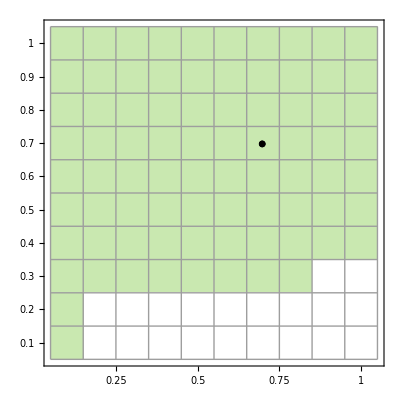

```mathematica
(* cFh from left-to-right, cFv from bottom-to-top *)
(* 0 = transition to mutualism, -1 = partner purged, 1 = antagonism *)
outcome={{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,-1,-1},
{0,-1,-1,-1,-1,-1,-1,-1,-1,-1},
{0,-1,-1,-1,-1,-1,-1,-1,-1,-1}};

(* Plot *)
Show[MatrixPlot[Reverse[outcome],AspectRatio->1,ColorRules->{-1->White,0->RGBColor[201/255,232/255,176/255],1->Gray},DataReversed->True,FrameStyle->Black,LabelStyle->Directive[FontSize->20],Mesh->True,FrameTicks->{{{{1,0.1},{2,0.2},{3,0.3},{4,0.4},{5,0.5},{6,0.6},{7,0.7},{8,0.8},{9,0.9},{10,1}},None},{{{0,0},{2.5,0.25},{5,0.5},{7.5,0.75},{10,1}},None}}],
ListPlot[{{9.25 0.7,9.25 0.7}},PlotMarkers->{Graphics[{EdgeForm[{Black,Thick}],FaceForm[Black],Disk[]}],0.05}]]
```